```mathematica
p=10;
s=0.05;
x0=0.5;
b=3;
c=1;
N0=4;
k=100;
```

```mathematica
original=NDSolve[{D[x[t],t]==-s*(1+p*x[t])*x[t]*(1-x[t]),D[n[t],t]==n[t]*((1+p*x[t])*(1+s*x[t]*(b-c))-n[t]/k),n[0]==N0,x[0]==x0},{x[t],n[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],n[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

```mathematica
approx=NDSolve[{D[x[t],t]==-s*(x[t]+(p-1)*x[t]*x[t]),D[n[t],t]==n[t]*((1+p*x[t])*(1+s*x[t]*(b-c))-n[t]/k),n[0]==N0,x[0]==x0},{x[t],n[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],n[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

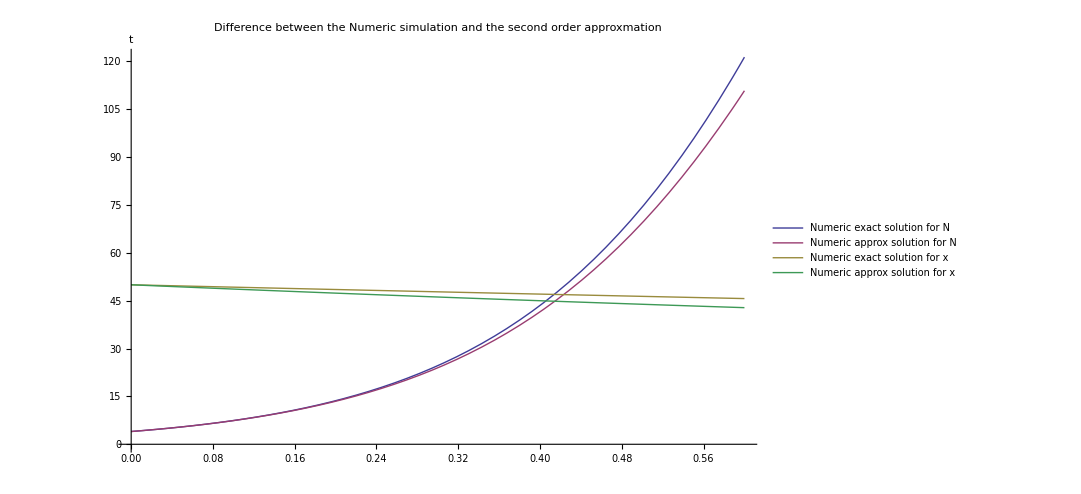

```mathematica
Plot[{Evaluate[n[t]/.original],Evaluate[n[t]/.approx],100*Evaluate[x[t]/.original],100*Evaluate[x[t]/.approx]},{t,0,0.6},PlotLegends->Placed[{"Numeric exact solution for N","Numeric approx solution for N","Numeric exact solution for x","Numeric approx solution for x"},{0.65,0.8}],AxesLabel->{"t"},PlotLabel->"Difference between the Numeric simulation and the second order approxmation",ImageSize->800]
```